# Algoritmy učení Demonstrace učení neuronu pomocí různých trénovacích algoritmů.

## Načtení knihovny NeuralNetworks

Nejdříve načteme knihovnu neuronových sítí.

```mathematica
<< NeuralNetworks`
```

Pokud pracujete v Mathematice 8.0, vypněte ještě zobrazování chybové hlášky Remove::rmnsm. Tuto hlášku vyhazují funkce knihovny NeuralNetworks. Na funkci knihovny toto nemá žádný vliv.

```mathematica
Off[Remove::rmnsm]
```

## Příprava trénovacích dat

Demonstraci provedeme na jednoduché neuronové sítí s jedním vstupem a jedním výstupem, žádnými skrytými vrstvami neuronů a sigmoidní aktivační funkcí. Jediný neuron v síti má 2 vstupy, na jednom je stále hodnota 1, na druhý jsou přiváděna vstupní data.

Vytvoříme tedy tuto síť:

```mathematica
fdfrwrd=InitializeFeedForwardNet[{{1}},{{1}},{},RandomInitialization->True,OutputNonlinearity->Sigmoid];
```

Nastavíme váhy vstupům neuronu na známou hodnotu 2 a -1:

```mathematica
fdfrwrd[[1]]={{{{2.},{-1.}}}};
```

Pomocí takto vytvořené sítě vygenerujeme trénovací data. Na vstup sítě přivedeme vstupní data a výstup sítě budeme považovat za správný výstup.

```mathematica
Ndata=50;
x=Table[{N[i]},{i,0,5,10/(Ndata-1)}];
y=fdfrwrd[x];
```

Z vygenerovaných dat si můžeme zobrazit energetickou funkci sítě:

```mathematica
criterion[a_?NumericQ,b_?NumericQ]:=(fdfrwrd[[1]]={{{{a},{b}}}};
Sqrt[(Transpose[#].#)&[y-fdfrwrd[x]]/Length[x]])[[1,1]]
surf=Plot3D[criterion[a,b],{a,-1,7},{b,-5,3},PlotPoints->20]
```

-Graphics3D-

Síť se během učení snaží minimalizovat hodnotu energetické funkce změnou vah vstupů neuronu. Data jsou připravena a můžeme přistoupit ke zkoušení trénovacích algoritmů.

## Levenberg-Marquardt algoritmus

Vytvoříme stejnou neuronovou síť jako při generování testovacích dat. Jejímu neuronu nastavíme váhy vstupů na -0,5 a -5. Takto vytvořenou síť necháme natrénovat pomocí Levenberg-Marquardt algoritmu.

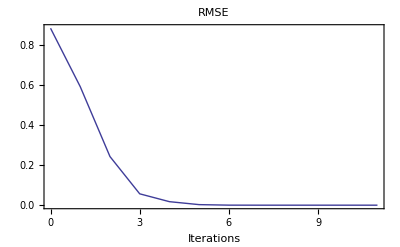

```mathematica
fdfrwrd2=fdfrwrd;
fdfrwrd2[[1]]={{{{-0.5},{-5}}}};
{fdfrwrd3,fitrecord}=NeuralFit[fdfrwrd2,x,y];
```

Zobrazíme si průběh učení sítě. Modré body zobrazují průběh učení. Čím je bod níže, tím lépe je síť naučena.

```mathematica
trajectory= 
Transpose[Append[Transpose[Map[Flatten,(ParameterRecord/.fitrecord[[2]])]],(CriterionValues/.fitrecord[[2]])+0.05]];
arrow2 = PhasePlot3D[surf,trajectory];
arrow = Graphics3D[{Red,Arrowheads[Medium],Arrow[trajectory]}];
trajectoryplot=ListPointPlot3D[trajectory,PlotStyle->AbsolutePointSize[8]];
Show[surf,trajectoryplot,arrow,PlotRange->All]
```

-Graphics3D-

Levenberg-Marquardt algoritmus dosáhl optimálního stavu po pěti iteracích.

## Gauss-Newton algoritmus

Vytvoříme stejnou neuronovou síť jako při generování testovacích dat. Jejímu neuronu nastavíme váhy vstupů na -0,5 a -5. Takto vytvořenou síť necháme natrénovat pomocí Gauss-Newton algoritmu.

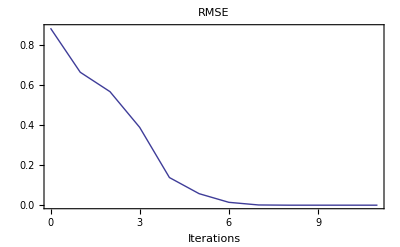

```mathematica
fdfrwrd2=fdfrwrd;
fdfrwrd2[[1]]={{{{-0.5},{-5}}}};
{fdfrwrd3,fitrecord}=NeuralFit[fdfrwrd2,x,y,Method->GaussNewton];
```

Zobrazíme si průběh učení sítě. Modré body zobrazují průběh učení. Čím je bod níže, tím lépe je síť naučena.

```mathematica
trajectory=Transpose[Append[Transpose[Map[Flatten,(ParameterRecord/.fitrecord[[2]])]],(CriterionValues/.fitrecord[[2]])+0.05]];
arrow = Graphics3D[{Red,Arrowheads[Medium],Arrow[trajectory]}];
trajectoryplot=ListPointPlot3D[trajectory,PlotStyle->AbsolutePointSize[8]];
Show[surf,trajectoryplot,arrow,PlotRange->All]
```

-Graphics3D-

Gauss-Newton algoritmus dosáhl ideálního stavu po sedmi iteracích.

## Algoritmus nejvyššího poklesu (Steepest Descent)

Vytvoříme stejnou neuronovou síť jako při generování testovacích dat. Jejímu neuronu nastavíme váhy vstupů na -0,5 a -5. Takto vytvořenou síť necháme natrénovat pomocí algoritmu nejvyššího poklesu.

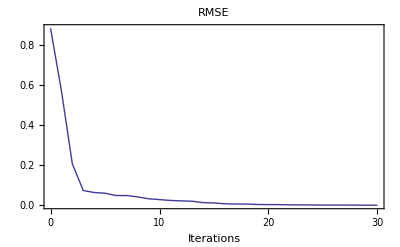

```mathematica
fdfrwrd2=fdfrwrd;
fdfrwrd2[[1]]={{{{-0.5},{-5}}}};
{fdfrwrd3,fitrecord}=NeuralFit[fdfrwrd2,x,y,Method->SteepestDescent];
```

Zobrazíme si průběh učení sítě. Modré body zobrazují průběh učení. Čím je bod níže, tím lépe je síť naučena.

```mathematica
trajectory=Transpose[Append[Transpose[Map[Flatten,(ParameterRecord/.fitrecord[[2]])]],(CriterionValues/.fitrecord[[2]])+0.05]];
arrow = Graphics3D[{Red,Arrowheads[Medium],Arrow[trajectory]}];
trajectoryplot=ListPointPlot3D[trajectory,PlotStyle->AbsolutePointSize[8]];
Show[surf,trajectoryplot,arrow,PlotRange->All]
```

-Graphics3D-

Algoritmus nenalezl ani po třiceti iteracích optimální řešení.

## Algoritmus zpětné propagace (Backpropagation)

Vytvoříme stejnou neuronovou síť jako při generování testovacích dat. Jejímu neuronu nastavíme váhy vstupů na -0,5 a -5. Takto vytvořenou síť necháme natrénovat pomocí algoritmu zpětné propagace.
Při použití algoritmu zpětné propagace je třeba nastavit velikost kroku a momentum (setrvačnost). Najít vhodné nastavení těchto parametrů není vždy snadné, různá nastavení mohou způsobit výrazné změny v průběhu učení.

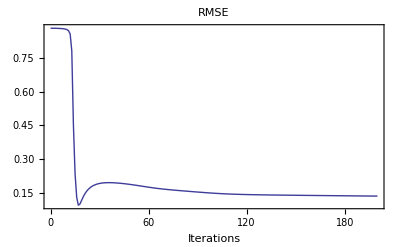

```mathematica
fdfrwrd2=fdfrwrd;
fdfrwrd2[[1]]={{{{-0.5},{-5}}}};
{fdfrwrd3,fitrecord}=NeuralFit[fdfrwrd2,x,y,200,Method->BackPropagation,StepLength->0.1,Momentum->0.9];
```

Zobrazíme si průběh učení sítě. Modré body zobrazují průběh učení. Čím je bod níže, tím lépe je síť naučena.

```mathematica
trajectory=Transpose[Append[Transpose[Map[Flatten,(ParameterRecord/.fitrecord[[2]])]],(CriterionValues/.fitrecord[[2]])+0.05]];
arrow = Graphics3D[{Red,Arrowheads[Medium],Arrow[trajectory]}];
trajectoryplot=ListPointPlot3D[trajectory,PlotStyle->AbsolutePointSize[8]];
Show[surf,trajectoryplot,arrow,PlotRange->All]
```

-Graphics3D-

Je patrné, že takto nastavený algoritmus (monentum 0.9 a délka kroku 0.1) nenalezl běhen 200 iterací optimální řešení.

Na následujícím grafu máte možnost měnit si velikost kroku a momenta. První spuštění může trvat delší dobu kvůli předpočítávání 3D grafu plochy.

```mathematica
surf2 = Plot3D[criterion[a, b], {a, -1, 45}, {b, -75, 20}, PlotPoints -> 65, 
    MaxRecursion -> 3]; 
Manipulate[fdfrwrd2 = fdfrwrd; fdfrwrd2[[1]] = {{{{-0.5}, {-5}}}}; 
   {fdfrwrd3, fitrecord} = NeuralFit[fdfrwrd2, x, y, 200, Method -> BackPropagation, 
     StepLength -> a, Momentum -> b, CriterionPlot -> False, CriterionLog -> False]; 
   trajectory = Transpose[Append[Transpose[Flatten /@ (ParameterRecord /. fitrecord[[2]])], 
      (CriterionValues /. fitrecord[[2]]) + 0.05]]; 
   arrow = Graphics3D[{Red, Arrowheads[Medium], Arrow[trajectory]}]; 
   maxx = Round[Max[Transpose[trajectory][[1]]]]; maxx= If[maxx<5,5,maxx];maxx=If[maxx>45,45,maxx];
   minx = Round[Min[Transpose[trajectory][[1]]]];  
   maxy = Round[Max[Transpose[trajectory][[2]]]]; maxy=If[maxy<0,0,maxy];maxy=If[maxy>20,20,maxy];
   miny = Round[Min[Transpose[trajectory][[2]]]]; miny=If[miny<-75,-75,miny];
   trajectoryplot = ListPointPlot3D[trajectory, PlotStyle -> AbsolutePointSize[8]]; 
   Show[surf2, trajectoryplot, arrow, PlotRange -> {{minx - 1, maxx + 1}, 
      {miny - 1, maxy + 1}, {0, 1}}], {{a, 0.1, "StephLength"}, 0.01, 0.999}, 
  {{b, 0.9, "Momentum"}, 0.01, 0.999}, ContinuousAction -> False]
```